```mathematica
(* Ищем u по f *)
```

```mathematica
pw=PageWidth/. Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
FortranForm[-0.11188827105317398 2.718281828459045^(-0.2357022603955158 (4.732050807568877+3. x)) (-26.513559170900876+5.449489742783178 2.718281828459045^(1.4142135623730951 x)+14.696938456699067 2.718281828459045^(0.4082482904638631+1.4142135623730951 x)-0.5505102572168221 2.718281828459045^(0.816496580927726+1.4142135623730951 x)-2.905547372312596 2.718281828459045^(1.1700499715209998+1.4142135623730951 x)+2.0650153761645464 2.718281828459045^(0.35355339059327373 (1.+4. x)))/. E^x_:>exp[x]]
SetOptions[$Output,PageWidth->pw];
```

(-0.11188827105317398*(-26.513559170900876 + 5.449489742783178*2.718281828459045**(1.4142135623730951*x) + 14.696938456699067*2.718281828459045**(0.4082482904638631 + 1.4142135623730951*x) - 0.5505102572168221*2.718281828459045**(0.816496580927726 + 1.4142135623730951*x) - 2.905547372312596*2.718281828459045**(1.1700499715209998 + 1.4142135623730951*x) + 2.0650153761645464*2.718281828459045**(0.35355339059327373*(1. + 4.*x))))/2.718281828459045**(0.2357022603955158*(4.732050807568877 + 3.*x))

```mathematica
f[x_]:=x;
```

-0.111888 2.71828^(-0.117851 (6.4641+6.9282 x)) (-17.6209+15.8338 2.71828^(1.63299 x)+1.13681 2.71828^(0.707107+1.63299 x)-3.11416 2.71828^(0.761802+1.63299 x)+0.55051 2.71828^(1.11536+1.63299 x)-0.55051 2.71828^(0.408248 (1.+4. x))-2.06502 2.71828^(0.707107+0.816497 x) x+2.90555 2.71828^(1.5236+0.816497 x) x-28.762 2.71828^(0.816497 x) x+0.208609 2.71828^(0.816497 (1.+x)) x)

-0.111888 2.71828^(-0.235702 (4.73205+3. x)) (-26.5136+5.44949 2.71828^(1.41421 x)+14.6969 2.71828^(0.408248+1.41421 x)-0.55051 2.71828^(0.816497+1.41421 x)-2.90555 2.71828^(1.17005+1.41421 x)+2.06502 2.71828^(0.353553 (1.+4. x)))+x

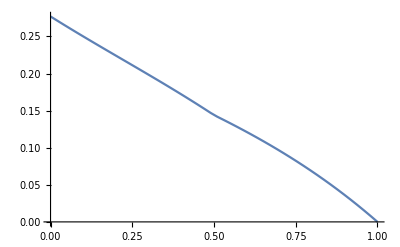

```mathematica
sol1[y_]:=(u[x]/.(DSolve[-D[3/2*D[u[x],x],x]+u[x]==f[x]&&u[0]+u'[0]==0,u,{x,0,1/2}]))[[1]]/.{x->y,C[1]->a};
sol2[y_]:=(u[x]/.(DSolve[-D[2*D[u[x],x],x]+u[x]==f[x]&&u[1]==0,u,{x,1/2,1}]))[[1]]/.{x->y,C[1]->b};
{aa,bb}={a,b}/.Solve[sol1[1/2]==sol2[1/2]&&3/2*sol1'[1/2]==2*sol2'[1/2]][[1]];
ssol1[y_]:=sol1[x]/.{x->y,a->aa,b->bb};
ssol2[y_]:=sol2[x]/.{x->y,a->aa,b->bb};
sol[x_]:=If[x<=1/2,ssol1[x],ssol2[x]];
N[FullSimplify[ssol1[x]]]
N[FullSimplify[ssol2[x]]]
Plot[sol[z],{z,0,1}]
```

-1/2 Sin[2 π x]^2 (-1+Cos[4 π x]+8 π (4 π (1+2 Cos[4 π x]) If[2 x≤1,1,3/2]+If[2 x≤1,0,0] Sin[4 π x]))

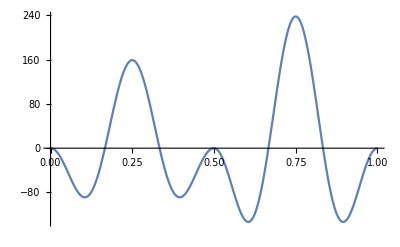

```mathematica
(* Ищем f по u *)

k[x_]:=If[x<=1/2,1,3/2];
g[x_]:=Sin[2*Pi*x]^4;
h[x_]:=-D[k[y]*g'[y],y]+g[y]/.{y->x} 
FullSimplify[h[x]]
Plot[h[x],{x,0,1}]
```